# Quantum Walk: A Mathematica notebook

## Find the original blog post, with a step - by - step tutorial, at https : // vicpina.com

## Parameters

```mathematica
pmax=45;(*max position*)
tmax=40;(*max time*)
```

```mathematica
listx=Table[p-(pmax+1),{p,1,2pmax+1}];
```

```mathematica
M=1/Sqrt[2]*{{1,1},{-1,1}};
```

## Initial conditions

```mathematica
x0=0;(*we use 0 as the origin*)
```

```mathematica
linitial[x_]:=0; linitial[x0]:=1/Sqrt[2];
rinitial[x_]:=0; rinitial[x0]:=I/Sqrt[2];
```

```mathematica
listl=Table[linitial[listx[[p]]],{p,1,2pmax+1}];
listr=Table[rinitial[listx[[p]]],{p,1,2pmax+1}];
```

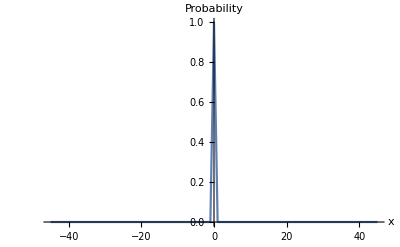

```mathematica
ListLinePlot[
Table[
{listx[[i]],
Abs[listl[[i]]]^2+Abs[listr[[i]]]^2},
{i,1,2 pmax+1}
],
AxesLabel->{"x","Probability"}
]
```

## Evolution of the Quantum Walk

```mathematica
lstate=Table[0,{j,1,tmax+1},{p,1,2 pmax+1}];
rstate=Table[0,{j,1,tmax+1},{p,1,2 pmax+1}];
```

```mathematica
lstate[[1]]=listl;
rstate[[1]]=listr;
```

```mathematica
Do[
Do[

lstate[[j+1,p]]=M[[1]][[1]] listl[[p+1]]+M[[1]][[2]] listr[[p-1]];
rstate[[j+1,p]]=M[[2]][[1]] listl[[p+1]]+M[[2]][[2]] listr[[p-1]],

{p,2,2 pmax}
];

listl=lstate[[j+1]];
listr=rstate[[j+1]],{j,1,tmax}

];
```

## Plotting our results

```mathematica
probDensity[x_]:=Abs[lstate[[tmax+1,x]]]^2+Abs[rstate[[tmax+1,x]]]^2
```

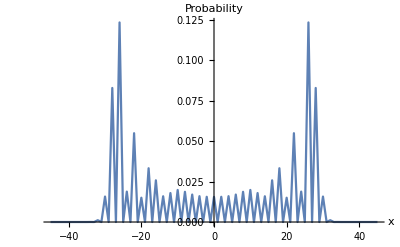

```mathematica
ListLinePlot[
Table[
{listx[[k]],
probDensity[k]},
{k,1,2pmax+1}
], 
PlotRange->{All,All},
PlotStyle->Default,
AxesLabel->{"x","Probability"}
]
```